```mathematica
blazers2016 =Import["/Users/erichegonzales/Projects/Probability/game_of_runs/Data/blazers_2016_17.csv", "Dataset"];
```

```mathematica
simple = Flatten[Map[If[StringContainsQ[#,"score"], 1, -1]&,blazers2016, {2}]]
```

```mathematica
counts2 = Counts[simple]
```

```mathematica
pScore = N[counts2[1] / Length[simple]]
pEmpty = N[counts2[-1] / Length[simple]]
```

0.395104

0.604896

```mathematica
streakBball[x_, pScore_, dep_]:= If[x==1,RandomChoice[{pScore-dep,1-pScore+dep}-> {1,-1}], RandomChoice[{pScore+dep,1-pScore-dep}-> {1, -1}]]
htWeighted [pScore_, n_,  dep_:0]:= NestList[streakBball[#,pScore, dep]&, 1, n-1]
```

```mathematica
med = Table[htWeighted[pScore, 1600], 10]
```

```mathematica
ext = Table[htWeighted[pScore, 1600, .025], 10]
```

```mathematica
medTwos= Map[SequenceCount[#, {1, -1}| {-1, 1}, Overlaps->True]&, med]
```

{777,759,785,753,765,726,791,758,753,753}

```mathematica
extTwos = Map[SequenceCount[#, {1, -1}| {-1, 1}, Overlaps->True]&, ext]
```

{823,842,801,769,803,786,822,799,787,816}

```mathematica
Tally[MapThread[Greater, {realTwos, medTwos}]]
```

{{True,5},{False,5}}

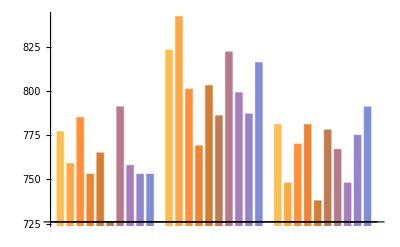

```mathematica
GraphicsRow[{ BarChart[{medTwos, extTwos, realTwos}, PlotRange->{Automatic, {Min[medTwos], Max[extTwos]}}]
}]
```

```mathematica
simpleChunks = Partition[Normal[simple], UpTo[1600]]
```

```mathematica
{1, 2, 3}[[;;-2]]
```

{1,2}

```mathematica
realTwos = Map[SequenceCount[#, {1, -1}| {-1, 1}, Overlaps->True]&, simpleChunks[[;;-2]]]
```

{781,748,770,781,738,778,767,748,775,791}